# Определение микропараметров I_2 с помощью спектрометра

## Калибровка спектрометра

Калибровку будем проводить по ртутной лампе. С помощью атласа линий ртути сопоставим линии излучения с номером пикселя.
-Graphics-

```mathematica
CalibrationHg=Import["C:\\Users\\alexn\\Documents\\GitHub\\Labs\\Phys_Labs\\5_sem\\Exam lab\\Calibration_Hg.xlsx"][[1]][[2;;All,1;;2]];
```

```mathematica
calibWaveLengths=CalibrationHg[[All,1]];
calibPixel=CalibrationHg[[All,2]];
calibrationHgReady=Transpose[ArrayReshape[AppendTo[calibPixel,calibWaveLengths],{2,Length[calibWaveLengths]}]];
```

Построим график зависимости длины волны от номера пикселя.

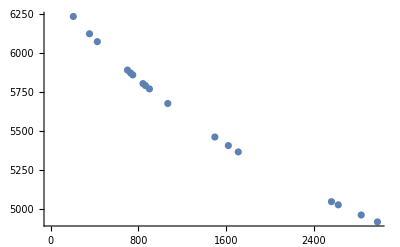

```mathematica
ListPlot[calibrationHgReady]
```

Аппроксимируем точки. Формула для калибровки имеет вид a+c/(x-b) .

```mathematica
fit=FindFit[calibrationHgReady,{a+c/(x-b),b<0},{a,b,c},x]
```

{a→2889.97,b→-4060.89,c→1.42866×10^7}

Получили параметры для аппроксимации.

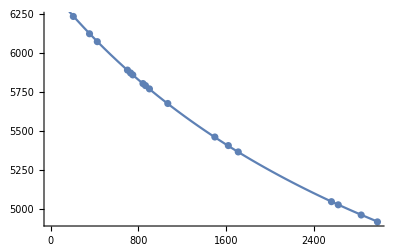

```mathematica
Show[ListPlot[calibrationHgReady],Plot[a+c/(x-b)/.fit,{x,0,3000}]]
```

Таким образом, получили функцию для калибровки :

```mathematica
Calibrate[λ_]:=a+c/(λ-b)/.fit;
```

## Выделение серий

Спектр лампы

Спектр I_2

```mathematica
lampSpectre=ReadList["C:\\Users\\alexn\\Documents\\GitHub\\Labs\\Phys_Labs\\5_sem\\Exam lab\\26_11_2018\\lamp2.txt",Number,WordSeparators->{"\t", "\n"}];
```

```mathematica
lampSpectre=ArrayReshape[lampSpectre,{Length[lampSpectre]/5,5}];
```

```mathematica
i2Spectre=ReadList["C:\\Users\\alexn\\Documents\\GitHub\\Labs\\Phys_Labs\\5_sem\\Exam lab\\26_11_2018\\i2-clear.txt",Number,WordSeparators->{"\t", "\n"}];
```

```mathematica
i2Spectre=ArrayReshape[i2Spectre,{Length[i2Spectre]/5,5}];
```

```mathematica
len=Length[lampSpectre]
```

30071

Спектр лампы (зеленая часть)

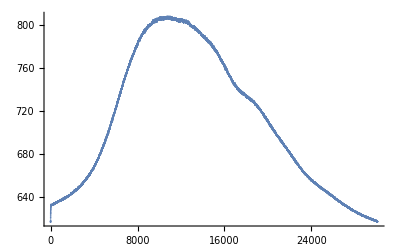

```mathematica
ListPlot[lampSpectre[[All,3]]]
```

```mathematica
peaks={};
```

Нехитрый инструмент для выделения пиков.

```mathematica
Manipulate[Grid[{p,{Show[ListLinePlot[Transpose[{i2Spectre[[x;;y,1]],i2Spectre[[x;;y,Channel+1]]}],ImageSize->Large],ListLinePlot[peaks,PlotStyle->Red]]},peaks}],{{x,0,"Begin"},1,len},{{y,Length[lampSpectre],"End"},1,len},{Channel,{1,2,3,4}},

Button["Add",AppendTo[peaks,MinimalBy[Transpose[{i2Spectre[[p[[1]]*10-50;;p[[1]]*10+50,1]],i2Spectre[[p[[1]]*10-50;;p[[1]]*10+50,Channel+1]]}],Last][[1]]]],
Button["Delete last",peaks=Delete[peaks,Length[peaks]]],
Button["Clear",peaks={}],
Button["To storage",AppendTo[peaksStorage,Transpose[peaks]],peaks={}],
{{p,{0,0}},Locator},
ContentSize->{600, 460}
]
```

Лучше всего нужные нам пики видны в зеленом канале.

```mathematica
peaks
```

{{1794.8,868.335},{1846.5,859.228},{1889.6,834.471},{1932.4,819.419},{1976.,804.468},{2019.8,789.04}}

```mathematica
Length[peaksStorage]
```

3

Зафиксируем полученные значения :

```mathematica
peaksStorage
```

{{{835.4,892.4,949.1,1004.9,1060.3,1115.6,1169.8,1223.4,1276.4,1330.,1381.5,1432.1,1483.1,1531.2,1581.1},{1247.51,1201.25,1148.66,1101.41,1058.51,1028.67,1003.38,1004.39,1006.37,993.664,1009.78,983.485,985.334,986.108,985.081}},{{956.7,1015.1,1073.1,1130.7,1187.4,1241.8,1299.5,1354.,1409.,1462.1,1515.6,1567.9,1619.,1668.5,1719.1,1767.6,1814.5,1862.1,1907.5,1951.1,1995.9,2038.,2079.1,2119.9,2157.4,2196.,2229.8,2267.,2300.8,2332.8,2364.,2394.1,2423.7,2450.4,2477.1,2501.4,2525.3,2548.1,2569.,2589.1,2608.6,2626.3,2643.5,2658.1,2674.2,2686.8,2697.9,2710.5,2722.3},{1395.07,1325.96,1236.08,1187.76,1120.29,1056.73,987.456,931.752,891.986,853.071,824.043,794.454,774.002,761.715,761.772,760.742,761.276,748.893,747.544,735.247,731.816,724.153,714.585,720.001,716.072,709.744,714.826,703.68,704.449,696.579,692.806,693.812,690.518,689.015,687.263,686.551,685.983,684.285,683.422,682.523,681.414,680.503,678.844,678.163,677.476,675.939,674.635,674.205,673.155}},{{375.8,431.3,487.5,545.8,603.4,659.1,717.9,773.4,828.8,883.5,938.2,992.2,1045.5,1101.1},{886.299,925.905,969.701,1017.38,1058.32,1107.77,1137.45,1152.62,1161.04,1166.28,1168.67,1178.03,1183.38,1191.38}},{{1794.8,1846.5,1889.6,1932.4,1976.,2019.8},{868.335,859.228,834.471,819.419,804.468,789.04}}}

```mathematica
(*Export["C:\\Users\\alexn\\Documents\\GitHub\\Labs\\Phys_Labs\\5_sem\\Exam lab\\peaksStorage.xlsx",peaksStorage]*)
```

C:\Users\alexn\Documents\GitHub\Labs\Phys_Labs\5_sem\Exam lab\peaksStorage.xlsx

Сведем все полученные серии на один график:

```mathematica
seriesPlots={};
For[i=1,i≤Length[peaksStorage],i++,
AppendTo[seriesPlots,ListLinePlot[Transpose[peaksStorage[[i]]],PlotStyle->Hue[i/Length[peaksStorage]]]]
]
```

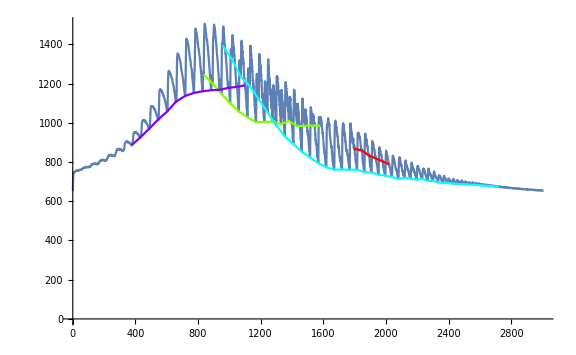

```mathematica
Show[ListLinePlot[Transpose[{i2Spectre[[All,1]],i2Spectre[[All,3]]}],ImageSize->Large],seriesPlots]
```

```mathematica
(*clearedSpectre={i2Spectre[[All,1]]};
AppendTo[clearedSpectre,Log[lampSpectre[[All,3]]/i2Spectre[[All,3]]]];
ListLinePlot[Transpose[clearedSpectre]]*)
```

Проведем калибровку полученного спектра

```mathematica
calibratedI2Spectre=Transpose[{Calibrate[i2Spectre[[All,1]]],i2Spectre[[All,2]],i2Spectre[[All,3]],i2Spectre[[All,4]],i2Spectre[[All,5]]}];
```

```mathematica
calibratedPeaksStorage={};
For[i=1,i≤ Length[peaksStorage],i++,
AppendTo[calibratedPeaksStorage,{Calibrate[peaksStorage[[i]][[1]]],peaksStorage[[i]][[2]]}]
]
```

```mathematica
calibratedSeriesPlots={};
For[i=1,i≤Length[calibratedPeaksStorage],i++,
AppendTo[calibratedSeriesPlots,ListLinePlot[Transpose[calibratedPeaksStorage[[i]]],PlotStyle->Hue[i/Length[calibratedPeaksStorage]]]]
]
```

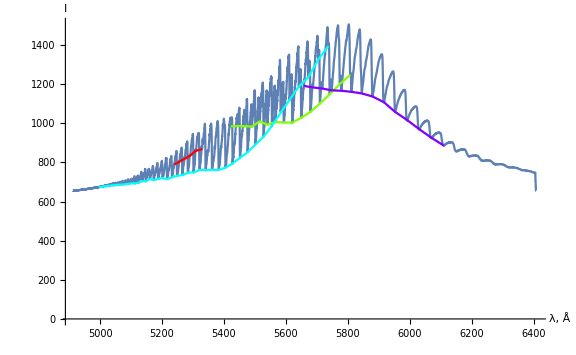

```mathematica
Show[ListLinePlot[Transpose[{calibratedI2Spectre[[All,1]],calibratedI2Spectre[[All,3]]}],ImageSize->Large,AxesLabel->{"λ, Å","I"}],calibratedSeriesPlots]
```

## Обработка результатов

Теперь построим зависимость энергии пика в серии от номера пика

```mathematica
calibratedPeaksStorage
```

{{{5807.82,5774.24,5741.6,5710.19,5679.68,5649.88,5621.28,5593.57,5566.73,5540.11,5515.04,5490.85,5466.93,5444.76,5422.17},{1247.51,1201.25,1148.66,1101.41,1058.51,1028.67,1003.38,1004.39,1006.37,993.664,1009.78,983.485,985.334,986.108,985.081}},{{5737.28,5704.52,5672.72,5641.85,5612.12,5584.19,5555.19,5528.37,5501.84,5476.73,5451.91,5428.11,5405.27,5383.54,5361.71,5341.14,5321.58,5302.03,5283.69,5266.33,5248.75,5232.47,5216.79,5201.43,5187.49,5173.31,5161.05,5147.69,5135.7,5124.46,5113.61,5103.24,5093.14,5084.1,5075.14,5067.05,5059.15,5051.67,5044.85,5038.34,5032.06,5026.39,5020.91,5016.28,5011.19,5007.23,5003.76,4999.82,4996.15},{1395.07,1325.96,1236.08,1187.76,1120.29,1056.73,987.456,931.752,891.986,853.071,824.043,794.454,774.002,761.715,761.772,760.742,761.276,748.893,747.544,735.247,731.816,724.153,714.585,720.001,716.072,709.744,714.826,703.68,704.449,696.579,692.806,693.812,690.518,689.015,687.263,686.551,685.983,684.285,683.422,682.523,681.414,680.503,678.844,678.163,677.476,675.939,674.635,674.205,673.155}},{{6110.08,6070.3,6031.,5991.25,5952.95,5916.8,5879.56,5845.24,5811.76,5779.43,5747.82,5717.28,5687.76,5657.63},{886.299,925.905,969.701,1017.38,1058.32,1107.77,1137.45,1152.62,1161.04,1166.28,1168.67,1178.03,1183.38,1191.38}},{{5329.76,5308.4,5290.89,5273.74,5256.52,5239.48},{868.335,859.228,834.471,819.419,804.468,789.04}}}

```mathematica
energyPeaks={};
For[i=1,i≤ Length[calibratedPeaksStorage],i++,
AppendTo[energyPeaks,UnitConvert[(h c)/Quantity[calibratedPeaksStorage[[i,1]],"Angstroms"]/.{h-> Quantity[1,"PlanckConstant"],c-> Quantity[1,"SpeedOfLight"]},"Electronvolts"]]
]
```

```mathematica
energyPeaks=QuantityMagnitude[energyPeaks]
```

{{2.13478,2.14719,2.1594,2.17128,2.18294,2.19446,2.20562,2.21655,2.22724,2.23794,2.24811,2.25801,2.2679,2.27713,2.28662},{2.16103,2.17344,2.18562,2.19758,2.20922,2.22027,2.23186,2.24269,2.25351,2.26384,2.27414,2.28412,2.29376,2.30302,2.3124,2.32131,2.32984,2.33843,2.34655,2.35428,2.36217,2.36952,2.37664,2.38366,2.39006,2.39661,2.40231,2.40854,2.41416,2.41946,2.42459,2.42952,2.43434,2.43866,2.44297,2.44687,2.45069,2.45432,2.45764,2.46082,2.46389,2.46667,2.46936,2.47164,2.47415,2.4761,2.47782,2.47977,2.48159},{2.02917,2.04247,2.05578,2.06942,2.08274,2.09546,2.10873,2.12111,2.13333,2.14527,2.15707,2.16859,2.17984,2.19145},{2.32626,2.33562,2.34335,2.35097,2.35867,2.36635}}

```mathematica
energyPeaks=SortBy[energyPeaks,First]
```

{{2.02917,2.04247,2.05578,2.06942,2.08274,2.09546,2.10873,2.12111,2.13333,2.14527,2.15707,2.16859,2.17984,2.19145},{2.13478,2.14719,2.1594,2.17128,2.18294,2.19446,2.20562,2.21655,2.22724,2.23794,2.24811,2.25801,2.2679,2.27713,2.28662},{2.16103,2.17344,2.18562,2.19758,2.20922,2.22027,2.23186,2.24269,2.25351,2.26384,2.27414,2.28412,2.29376,2.30302,2.3124,2.32131,2.32984,2.33843,2.34655,2.35428,2.36217,2.36952,2.37664,2.38366,2.39006,2.39661,2.40231,2.40854,2.41416,2.41946,2.42459,2.42952,2.43434,2.43866,2.44297,2.44687,2.45069,2.45432,2.45764,2.46082,2.46389,2.46667,2.46936,2.47164,2.47415,2.4761,2.47782,2.47977,2.48159},{2.32626,2.33562,2.34335,2.35097,2.35867,2.36635}}

```mathematica
energyPeaksNumerated={};
series={};
For[i=1,i≤ Length[energyPeaks],i++,
For[j=1,j≤ Length[energyPeaks[[i]]],j++,
AppendTo[series,{j,energyPeaks[[i,j]]}];
];
AppendTo[energyPeaksNumerated,series];
series={};
]
```

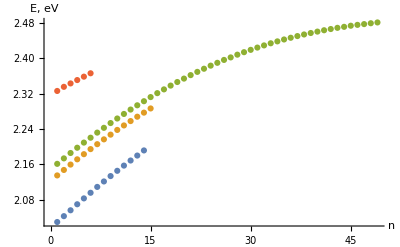

```mathematica
ListPlot[energyPeaksNumerated,AxesLabel->{"n","E, eV"}]
```

Теперь подберем наилучшие сдвиги. Для этого построим графики ΔE(n)

```mathematica
deltasH={};
For[i=2,i≤Length[energyPeaksNumerated],i++,
AppendTo[deltasH,{Table[a,{a,Min[Length[Transpose[energyPeaksNumerated[[i]]][[1]]],Length[Transpose[energyPeaksNumerated[[i-1]]][[1]]]]}],Transpose[energyPeaksNumerated[[i]]][[2]][[1;;Min[Length[energyPeaksNumerated[[i]]],Length[energyPeaksNumerated[[i-1]]]]]]-Transpose[energyPeaksNumerated[[i-1]]][[2]][[1;;Min[Length[energyPeaksNumerated[[i]]],Length[energyPeaksNumerated[[i-1]]]]]]}
]
]
```

```mathematica
deltas={};
For[i=1,i≤ Length[deltasH],i++,
AppendTo[deltas,Transpose[deltasH[[i]]]]
]
```

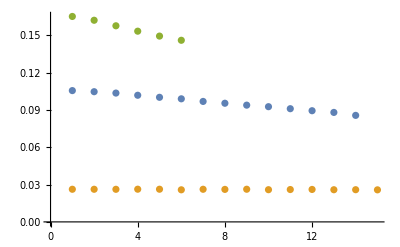

```mathematica
ListPlot[deltas]
```

Устанавливая значения сдвигов, добьемся чтобы линии ΔE были максимально горизонтальными. Сделаем еще один небольшой инструмент для подбора сдвигов.

```mathematica
offsets={};
Manipulate[
Grid[{{Show[
ListPlot[energyPeaksNumerated[[1]]+Table[{o1,0},Length[energyPeaksNumerated[[1]]]],AxesLabel->{"n","E, eV"},ImageSize->Large],
ListPlot[energyPeaksNumerated[[2]]+Table[{o2,0},Length[energyPeaksNumerated[[2]]]],PlotStyle->Orange],
ListPlot[energyPeaksNumerated[[3]]+Table[{o3,0},Length[energyPeaksNumerated[[3]]]],PlotStyle->Green],
ListPlot[energyPeaksNumerated[[4]]+Table[{o4,0},Length[energyPeaksNumerated[[4]]]],PlotStyle->Red],
PlotRange->All
]},{Show[
ListPlot[
energyPeaks[[1,Max[o1,o2]-o1+1;;Max[o1,o2]-o1+1+Min[Length[energyPeaks[[1]]]-(Max[o1,o2]-o1+1),Length[energyPeaks[[2]]]-(Max[o1,o2]-o2+1)]]]-
energyPeaks[[2,Max[o1,o2]-o2+1;;Max[o1,o2]-o2+1+Min[Length[energyPeaks[[1]]]-(Max[o1,o2]-o1+1),Length[energyPeaks[[2]]]-(Max[o1,o2]-o2+1)]]],ImageSize->Large
],
ListPlot[
energyPeaks[[2,Max[o2,o3]-o2+1;;Max[o2,o3]-o2+1+Min[Length[energyPeaks[[2]]]-(Max[o2,o3]-o2+1),Length[energyPeaks[[3]]]-(Max[o2,o3]-o3+1)]]]-
energyPeaks[[3,Max[o2,o3]-o3+1;;Max[o2,o3]-o3+1+Min[Length[energyPeaks[[2]]]-(Max[o2,o3]-o2+1),Length[energyPeaks[[3]]]-(Max[o2,o3]-o3+1)]]],PlotStyle->Green,ImageSize->Large
],
ListPlot[
energyPeaks[[3,Max[o3,o4]-o3+1;;Max[o3,o4]-o3+1+Min[Length[energyPeaks[[3]]]-(Max[o3,o4]-o3+1),Length[energyPeaks[[4]]]-(Max[o3,o4]-o4+1)]]]-
energyPeaks[[4,Max[o3,o4]-o4+1;;Max[o3,o4]-o4+1+Min[Length[energyPeaks[[3]]]-(Max[o3,o4]-o3+1),Length[energyPeaks[[4]]]-(Max[o3,o4]-o4+1)]]],PlotStyle->Red,ImageSize->Large
],PlotRange->{{0,20},{-0.05,0}}
]}}],
{{o1,0,"Offset 1"},0,25,1},
{{o2,0,"Offset 2"},0,25,1},
{{o3,0,"Offset 3"},0,25,1},
{{o4,0,"Offset 4"},0,25,1},
Button["Save offsets",offsets={o1,o2,o3,o4}]
]
```

Значения n таким образом

```mathematica
offsets
```

{0,6,6,20}